## Derivation of scattering contributions from a thin rigid rod.

```mathematica
$Assumptions:={L>0, Rg>0,q>0}
```

#### Rod model

We regard a rod of length L with a homogeneous scattering length along its contour. 

Compared to a polymer, now the spatial distance and the contour distance between two scatterers is exactly the same. However, we have to remember that the rod can be orientated in all directions.

#### Lets now calculate all the relevant mean - square distance measures explicitly

Lets assume the rod has coordinates (-L/2,0,0) to (+L/2,0,0)  hence we can describe it by (x,0,0) making square distances one dimensional.
The averaged square distance from one end to any internal point is:

```mathematica
<[R-R(end1)]^2> =
```

```mathematica
1/L∫_(-L/2)^(+L/2) (x-(-L/2))^2 ⅆx
```

L^2/3

```mathematica
<[R-R(end2)]^2> =
```

```mathematica
1/L∫_(-L/2)^(+L/2) (x-(+L/2))^2 ⅆx
```

L^2/3

```mathematica
<[R-Rmid]^2>
```

```mathematica
1/L∫_(-L/2)^(+L/2) (x)^2 ⅆx
```

L^2/12

The averaged distance between a pair of points along the chain, here I divide by two since x1,x2 and x2,x1 gives the same distance twice which provides the radius of gyration:

```mathematica
<[Ri-Rj]^2> =  (unique i,j)
```

```mathematica
1/(2 L^2)∫_(-L/2)^(+L/2) ∫_(-L/2)^(+L/2) (x2-x1)^2 ⅆx1ⅆx2
```

L^2/12

```mathematica
<[Ri-Rj]^2> =  (any i,j)
```

```mathematica
1/L^2∫_(-L/2)^(+L/2) ∫_(-L/2)^(+L/2) (x2-x1)^2 ⅆx1ⅆx2
```

L^2/6

#### Scattering Form Factor

Using the Debye formula, we can calculate the scattering contribution between any two scatterers along the rod, the Debye formula takes care of the orientational average:

```mathematica
1/L^2∫_(-L/2)^(+L/2) ∫_(-L/2)^(+L/2) Sin[q Abs[x2-x1]]/(q Abs[x2-x1])ⅆx1ⅆx2
```

(2 (-1+Cos[L q]+L q SinIntegral[L q]))/(L^2 q^2)

It seems that x = q L is a good dimensionless variable .

```mathematica
F=1/L^2∫_(-L/2)^(+L/2) ∫_(-L/2)^(+L/2) Sin[q Abs[x2-x1]]/(q Abs[x2-x1])ⅆx1ⅆx2/.q->x/L
```

(2 (-1+Cos[x]+x SinIntegral[x]))/x^2

SinIntegral[z]) = Si(z)=∫_0^z sin(t)/t dt. 
Reference for this form factor: T. Neugebauer, Ann. Phys. (Leipzig) 42, 509 (1943). P. I. Teixeira, D. J. Read, and T. C. B. McLeish, J. Chem. Phys. 126,
074901 (2007).

#### Form factor amplitude relative to ends

```mathematica
Aend1=1/L∫_(-L/2)^(+L/2) Sin[q (x+L/2)]/(q (x+L/2))ⅆx/.q->x/L
```

SinIntegral[x]/x

```mathematica
Aend2=1/L∫_(-L/2)^(+L/2) Sin[q (x-L/2)]/(q (x-L/2))ⅆx/.q->x/L
```

SinIntegral[x]/x

Due to symmetry, these gives the same result, which is not that obvious given the two expressions above, but e.g. Taylor expanding shows the they match term-by-term as expected.
 
Reference : “A formalism for scattering of complex composite structures. II. Distributed reference points.” C . Svaneborg and J . S . Pedersen J . Chem . Phys . 136, 154907 (2012) DOI : http://dx.doi.org/10.1063/1.3701737

#### Phase factor between the ends

```mathematica
Psiend1end2=Sin[q L]/(q L)/.q->x/L //Simplify
```

Sin[x]/x

#### Scattering terms involving a mIddle reference point.

Assuming we place a reference point at the middle of the rod at (0, 0, 0) we get the following form factor amplitude, and phase factor .

```mathematica
Amiddle=1/L∫_(-L/2)^(+L/2) Sin[q (x-0)]/(q (x-0))ⅆx/.q->x/L
```

(2 SinIntegral[x/2])/x

```mathematica
Psimiddle2end=Sin[q L/2]/(q L/2)/.q->x/L //Simplify
```

(2 Sin[x/2])/x

#### Contour distributed reference points :

We need to calculate the scattering between a reference point at x1 uniformly distributed in [-L/2,+L/2] and a scatterer at x2 uniformly distributed in [-L/2,+L/2] :

```mathematica
Acontour=1/L^2∫_(-L/2)^(+L/2) ∫_(-L/2)^(+L/2) Sin[q Abs[x2-x1]]/(q Abs[x2-x1])ⅆx1ⅆx2/.q->x/L //Simplify
```

(2 (-1+Cos[x]+x SinIntegral[x]))/x^2

To calculate the average phase factor between the end x1=-L/2 and a uniformly distributed reference point at x2:

```mathematica
Psiend1contour=1/L∫_(-L/2)^(+L/2) Sin[q Abs[x2-x1]]/(q Abs[x2-x1])ⅆx2/.x1->-L/2/.q->x/L
```

SinIntegral[x]/x

```mathematica
Psiend2contour=1/L∫_(-L/2)^(+L/2) Sin[q Abs[x2-x1]]/(q Abs[x2-x1])ⅆx1/.x2->L/2/.q->x/L
```

1/(8 x)(2 CosIntegral[x] Sin[x]+2 Log[4] Sin[x]-2 Log[x] Sin[x]+6 SinIntegral[x]-2 Cos[x] SinIntegral[x]-√π x Cos[x/2] Hypergeometric0F1Regularized^(1,0)[3/2,-x^2/16])

Again an ugly expression, which is identical to Psi_end1contour. 
To calculate the phase factor between x1 and x2 uniformly distributed along the rod, we get the form factor again:

```mathematica
Psicontour2contour=1/L^2∫_(-L/2)^(+L/2) ∫_(-L/2)^(+L/2) Sin[q Abs[x2-x1]]/(q Abs[x2-x1])ⅆx1ⅆx2/.q->x/L //Simplify
```

(2 (-1+Cos[x]+x SinIntegral[x]))/x^2

The final missing expression is the average phase factor between a random along the contour (x1 in [-L/2, L/2]) and the middle point x2 = 0 :

```mathematica
Psicontour2middle=1/L∫_(-L/2)^(+L/2) Sin[q Abs[x2-x1]]/(q Abs[x2-x1])ⅆx1/.x2->0/.q->x/L
```

(2 SinIntegral[x/2])/x

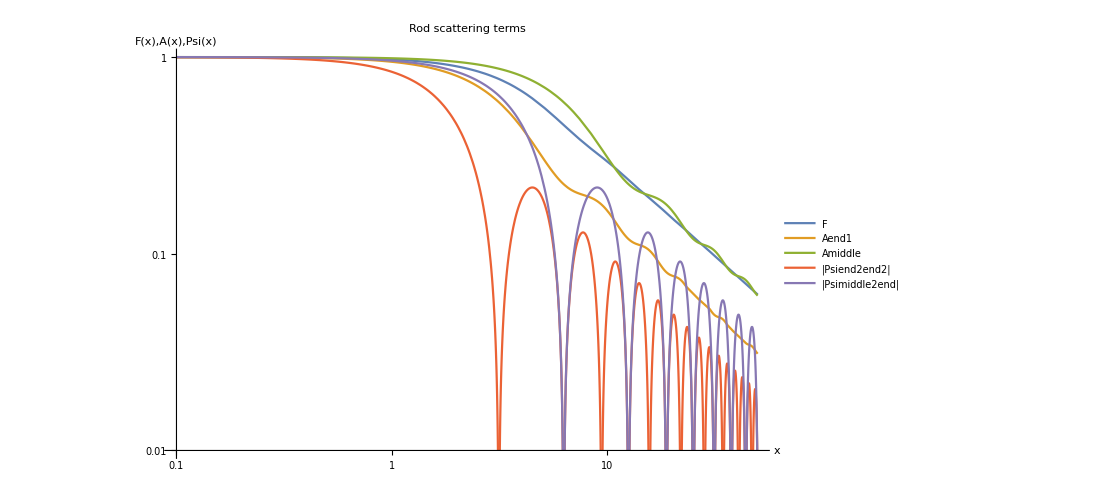

```mathematica
LogLogPlot[{F,Aend1,Amiddle,Abs[Psiend1end2],Abs[Psimiddle2end]},{x,0.1,50},PlotLabel-> "Rod scattering terms",AxesLabel-> {"x","F(x),A(x),Psi(x)"},PlotLegends-> {"F","Aend1","Amiddle","|Psiend2end2|","|Psimiddle2end|"},PlotRange-> {0.01,1}]
```

#### Guinier - expansions

Above we derived the mean - square distances explicitly. Here we show how to obtain these from a Guinier expansion of the various scattering terms.

The Guinier expansion of F is
1 - q^2 Rg^2 / 3 + O(q^4)

```mathematica
Series[F/.x-> q L,{q,0,3}]
```

1-(L^2 q^2)/36+O[q]^4

Hence to isolate the radius of gyration in the series:

```mathematica
(3(1-Normal[Series[F/.x-> q L,{q,0,3}]]))/q^2
```

L^2/12

This works as expected.

The Guinier expansion of A and Psi are :   1 - q^2 <distance^2> / 6 + O(q^4).

```mathematica
<[R-Rend]^2>
```

```mathematica
(6(1-Normal[Series[SinIntegral[x]/x/.x-> q L,{q,0,3}]]))/q^2
```

L^2/3

```mathematica
<[R-Rmid]^2>
```

```mathematica
(6(1-Normal[Series[(2 SinIntegral[x/2])/x/.x-> q L,{q,0,3}]]))/q^2
```

L^2/12

```mathematica
<[Rend-Rmid]^2>
```

```mathematica
(6(1-Normal[Series[(2 Sin[x/2])/x/.x-> q L,{q,0,3}]]))/q^2
```

L^2/4

```mathematica
<[Ri-Rj]^2>
```

```mathematica
1/q^2 6(1-Normal[Series[(2 (-1+Cos[x]+x SinIntegral[x]))/x^2/.x-> q L,{q,0,3}]])
```

L^2/6

```mathematica
Series[SinIntegral[x]/x,{x,0,6}]
```

1-x^2/18+x^4/600-x^6/35280+O[x]^7

```mathematica
D[SinIntegral[x]/x,x]
```

Sinc[x]/x-SinIntegral[x]/x^2

```mathematica
Series[D[SinIntegral[x]/x,x],{x,0,6}]
```

-x/9+x^3/150-x^5/5880+O[x]^7

#### Save example data to file for Validation :

```mathematica
SaveFunction[func_,filename_,NN_,qmin_,qmax_]:=Module[{},Export[filename,{#,N[func/.q-> #]}&/@Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]]]
```

```mathematica
SaveFunction[F/.x-> q  L/.L->1 ,"/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/F.dat",200,0.01,20]
SaveFunction[Aend1/.x-> q  L/.L->1 ,"/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/A_end.dat",200,0.01,20]
SaveFunction[Amiddle/.x-> q  L/.L->1 ,"/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/A_middle.dat",200,0.01,20]
SaveFunction[Psiend1end2/.x-> q  L/.L->1 ,"/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/Psi_end2end.dat",200,0.01,20]
SaveFunction[Psimiddle2end/.x-> q  L/.L->1 ,"/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/Psi_end2middle.dat",200,0.01,20]
SaveFunction[Psicontour2middle/.x-> q  L/.L->1 ,"/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/Psi_contour2middle.dat",200,0.01,20]
```

/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/F.dat

/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/A_end.dat

/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/A_middle.dat

/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/Psi_end2end.dat

/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/Psi_end2middle.dat

/home/zqex/source/SEB/source/Validation/ThinRod_mathematica/Psi_contour2middle.dat